In this notebook is simulated the activation regulation with GA and the three-stage model (burst expression). The notebook has two parts:
1. To evaluate the “sensitivity” to the whole set the parameters. With an arbitrary start point to calculate the estimates (FF, CV2,Mean) (30% of the total number of iterations), and different number of iterations to get a final t of 1500. 
2. To evaluate 4 specific regions or set of parameters

## Parameters for the two sessions

These are the ranges of values for parameters variation. The range of each parameter is divided into smaller ranges (subRanges). In this way the complete range is evaluated in parallel files each one with a subRange of parameters values.

```mathematica
name=0.5; (* This is the last value of the range for the parameter being evluated *)
kgs=Range[0.01,1,0.01];
γgs=Range[0.02,name,0.02]; (* subRanges: 0.02-0.5, 0.52-1.0, 1.02-1.5, 1.52-2 *)
γms=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
γps=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
parametro="γg";(* With the name of the second parameter is named the output file *)
```

These are the default values of parameters

```mathematica
{kgA,kgB}={0.01158,0.01158};(* Gene activation rate (t^-1)*)
{γgA,γgB}= {2.082,2.082};(* Gene desactivation rate (t^-1) *)
{kmA,kmB}={0.696,0.696};(* mRNA production rate(molecules*t^-1) *)
{γmA,γmB}={0.02082  ,0.02082 } ;(* mRNA degradation rate(molecules*t^-1) *)
{kpA,kpB}={1.386,1.386};(* Protein production rate (molecules*t^-1) *)
{γpA,γpB}={0.02082  ,0.02082 };(* Protein degradation rate (molecules*t^-1) *)
kAB=100;(* Michaelis-Menten constant *)
h=3 (* Hill's constant *);
{bmA,bmB}={kmA/(γgA+kgA),kmB/(γgB+kgB)};(* Burst size mean (molecules-mRNA) *)
{bpA,bpB}={kpA/γmA,kpB/γmB};(* Burst size mean (molecules-proteins) *)
```

## Functions for the two sessions

These are the reactions (changesByRXN) and propensity functions (pF) of the GA for the specific regulation system: A: Activator -> B : Activated gene

```mathematica
changesByRXN=Function/@<|1->{#1,#2,#3,#4,#5-1,#6+1,#7,#8},2->{#1,#2,#3,#4,#5+1,#6-1,#7,#8},3->{#1+1,#2,#3,#4,#5,#6,#7,#8},4->{#1,#2+1,#3,#4,#5,#6,#7,#8},5->{#1-1,#2,#3,#4,#5,#6,#7,#8},6->{#1,#2-1,#3,#4,#5,#6,#7,#8},7->{#1,#2,#3,#4,#5,#6,#7-1,#8+1},8->{#1,#2,#3,#4,#5,#6,#7+1,#8-1},9->{#1,#2,#3+1,#4,#5,#6,#7,#8},10->{#1,#2,#3,#4+1,#5,#6,#7,#8},11->{#1,#2,#3-1,#4,#5,#6,#7,#8},12->{#1,#2,#3,#4-1,#5,#6,#7,#8}|>;(*Each hash represents a specie: mRNAA-proteinA-mRNAB-proteinB-da0A:promoterInactivatedA-da1A:promoterActivatedA-db0B-db1B
   The numbers are the next reactions: 1-7-> Activation,2-8-> Desactivation, 3-4-9-10-> Synthesis,5-6-11-12-> Degradation*)

pF=Compile[{{h,_Real},{kAB,_Real},{kgA,_Real},{γgA,_Real},{kmA,_Real},{γmA,_Real},{kpA,_Real},{γpA,_Real},{kgB,_Real},{γgB,_Real},{kmB,_Real},{γmB,_Real},{kpB,_Real},{γpB,_Real},{mRNAA,_Integer},{proteinA,_Integer},{mRNAB,_Integer},{proteinB,_Integer},{d0A,_Integer},{d1A,_Integer},{d0B,_Integer},{d1B,_Integer}},{d0A*kgA,d1A*γgA,d1A*kmA+0.01,kpA*mRNAA,mRNAA*γmA,γpA*proteinA,d0B*kgB(proteinA^h/(kAB+proteinA^h)),d1B*γgB,d1B*kmB+0.01,kpB*mRNAB,mRNAB*γmB,γpB*proteinB},RuntimeAttributes->{Listable},Parallelization->True];
```

This is equal for all  sub-circuits

```mathematica
ff[dato_]:=N[Variance[dato]/Mean[dato]];(* Fano Factor for noise measure *)
expressionNoise[data_]:=N[Variance[data]/Mean[data]^2](* Squared Coefficient of Variation for noise measure *)
```

```mathematica
(* This is the algorithm to estimate the Steady State start from Kelly and Hedengren 2013 *)steadyStateStart[window_,listData_]:=Block[{n,dataByWindow,mPorVentana,μ,sd,probabilidades},
n=Floor[Length[#]/window]&[listData];
dataByWindow=Partition[#,n]&[listData[[All,2]]];mPorVentana=Map[Mean[#[[2;;All]]-#[[1;;-2]]]&,dataByWindow];μ=MapThread[(1/n)(Total[#1]-#2*Total[Range[1,n](*tPorVentana*)])&,{dataByWindow,mPorVentana}];sd=Table[Sqrt[(1/(n-2))*Sum[(dataByWindow[[i,j]]-mPorVentana[[i]]*j-μ[[i]])^2,{j,1,Length[dataByWindow[[i]]]}]],{i,window}];probabilidades=Map[Total[#]/n&,Table[If[Abs[dataByWindow[[i,j]]-μ[[i]]]≤sd[[i]],1,0],{i,window},{j,1,n}]]//N;
((Position[probabilidades,x_/;x>0.1][[1,1]]-1)*n)+1]
```

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins with log scale *)plotsLogExpression[rep_,ini_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,mRNAffcv2MeanI_,proteinffcv2MeanI_,parametros_]:=Module[{datesListAm,datesListAp,datesListBm,datesListBp},
SetOptions[ListLogPlot,Frame-> True,ImageSize->Medium,Joined->True];

{datesListAm,datesListAp,datesListBm,datesListBp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,4}];{ListLogPlot[datesListAm[[ini;;]],PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLogPlot[datesListBm[[ini;;]],PlotStyle->
RGBColor[0.5,0.99,1],FrameLabel->{"time","mRNA B molecules"},PlotLabel->labelB],
ListLogPlot[datesListAp[[ini;;]],PlotStyle->
RGBColor[0.2,.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp],
ListLogPlot[datesListBp[[ini;;]],PlotStyle->
RGBColor[0.3,.09,0.7],FrameLabel->{"time","protein B molecules"},PlotLabel->labelBp]}]
```

## S1: All range parameters values

### Parameters

```mathematica
iteraciones2=400000; (* Number of algorithm iterations *)
replicas2=5; (* Number of times the algorithm is run *)
```

### Simulation

```mathematica
(* Launch the number of kernels in which you will parallelize the simulation *)
LaunchKernels[44]
```

This function runs the GA algorithm and processes the output according to the previous functions.

```mathematica
DistributeDefinitions[changesByRXN,pF,ff,expressionNoise,iteraciones1,h,kAB,kgA,γgA,kmA,γmA,kpA,γpA,kgB,γgB,kmB,γmB,kpB,γpB];
(*List by parameters*)
mRNAffcv2ListA={};
proteinffcv2ListA={};
mRNAffcv2ListI={};
proteinffcv2ListI={};

Do[
(*List by replicates*)
listEstimatemRNAA={};
listEstimateproteinA={};
listEstimatemRNAI={};
listEstimateproteinI={};
 listDataAndTimeT={};

SetSharedVariable[listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI, listDataAndTimeT];

ParallelDo[

listDataAndTime = CreateDataStructure["OrderedHashSet"];
abundancia={1,1,1,1,1,0,1,0}(*mRNAA,proteinA,mRNAI,proteinI,da0A,da1A,db0I,db1I*);
t=0;

Do[
τis=Map[If[#>0,RandomVariate[ExponentialDistribution[#]],∞]&,pF[h,kAB,kgA,γgA,kmA,γmA,kpA,γpA,kgB,γgB,kmB,γmB,kpB,γpB,Sequence@@abundancia]];
reactionAndτμ={FirstPosition[#,Min[#]],Min[#]}&[τis];abundancia=Through[{reactionAndτμ[[1]]/.changesByRXN}[[1,1]]@@abundancia][[1]];t=t+reactionAndτμ[[2]];         
 listDataAndTime["Union", {{t, abundancia}}];
            If[Length[#]>3&&#[[2]]==5&[IntegerDigits[Round[t]]](* para que Break a los 1500*), Break[]],iteraciones1 ];

  listData = Normal[listDataAndTime][[All, 2]];
        ini =Echo@Round[(Length[listData]*30)/100.] (*el estado estable se considera depués del 30% de iteraciones *);
(*ini = steadyStateStart[window,listData];*)
{mRNAffcv2ItA,proteinffcv2ItA}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]},{i,{listData[[ini;;All,1]],
listData[[ini;;All,2]]}}];
{mRNAffcv2ItI,proteinffcv2ItI}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]},{i,{listData[[ini;;All,3]],
listData[[ini;;All,4]]}}];

AppendTo[listEstimatemRNAA,mRNAffcv2ItA];
AppendTo[listEstimateproteinA,proteinffcv2ItA];
AppendTo[listEstimatemRNAI,mRNAffcv2ItI];
AppendTo[listEstimateproteinI,proteinffcv2ItI];
AppendTo[listDataAndTimeT,listDataAndTime];,


replicas1];

AppendTo[mRNAffcv2ListA,Mean[listEstimatemRNAA]];
AppendTo[proteinffcv2ListA,Mean[listEstimateproteinA]];
AppendTo[mRNAffcv2ListI,Mean[listEstimatemRNAI]];
AppendTo[proteinffcv2ListI,Mean[listEstimateproteinI]];,

    
 {kgA,{1}},{γgA,{0.01}}]; (*CAMBIAR AQUI EN EL .m*)
```

>> 41098

>> 41376

>> 42697

>> 42688

```mathematica
(* CAMBIAR AQUI EN EL .m _Cuando cambiamos A *****************)
```

```mathematica
Export["controlAIGAA_AA"<>parametro<>ToString[name],{mRNAffcv2ListA,proteinffcv2ListA},"CSV"];
Export["controlAIGAA_IA"<>parametro<>ToString[name],{mRNAffcv2ListI,proteinffcv2ListI},"CSV"];
```

```mathematica
(* CAMBIAR AQUI EN EL .m _Cuando cambiamos I *****************)
```

```mathematica
Export["controlAIGAI_AA"<>parametro<>ToString[name],{mRNAffcv2ListA,proteinffcv2ListA},"CSV"];
Export["controlAIGAI_IA"<>parametro<>ToString[name],{mRNAffcv2ListI,proteinffcv2ListI},"CSV"];
```

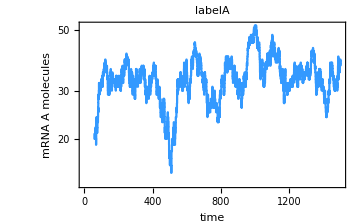
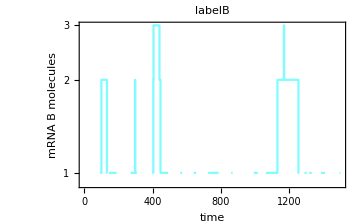
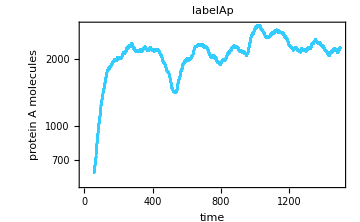
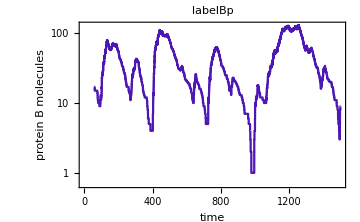
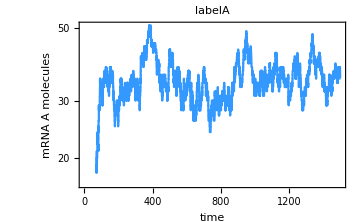
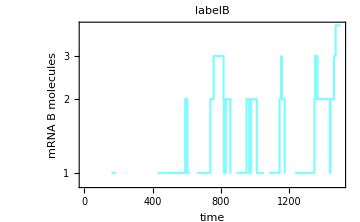
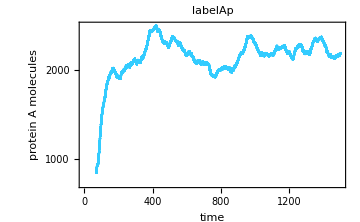
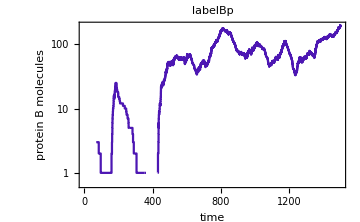
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
listDataAndTimeTN=Normal/@listDataAndTimeT;
MapThread[plotsLogExpression[#1,#2,listDataAndTimeTN,"","","","",""]&,{Range[1,replicas1],{1394,2203,1605,1668}}]
```

## S2: Evaluation by regions

### Parameters

```mathematica
iteraciones2=400000; (* Number of algorithm iterations *)
replicas2=500; (* Number of times the algorithm is run *)
rep=1; (* Some plots are made with the output of this replicate*)
lagStep=10; (* Lag time for the Autocorrelation plot *)
species=4;(*mRNA genA/B protein genA/B*)
```

### Functions

These functions make different plots of the temporal genes expression

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins *)plotsExpression[rep_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,mRNAffcv2MeanI_,proteinffcv2MeanI_,parametros_]:=Module[{datesListAm,datesListAp,datesListBm,datesListBp},
SetOptions[ListLinePlot,Frame-> True,ImageSize->Medium];

{datesListAm,datesListAp,datesListBm,datesListBp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,4}];{ListLinePlot[datesListAm,PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLinePlot[datesListBm,PlotStyle->
RGBColor[0.5,0.99,1],FrameLabel->{"time","mRNA B molecules"},PlotLabel->labelB],
ListLinePlot[datesListAp,PlotStyle->
RGBColor[0.2,.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp],
ListLinePlot[datesListBp,PlotStyle->
RGBColor[0.3,.09,0.7],FrameLabel->{"time","protein B molecules"},PlotLabel->labelBp]}]
```

```mathematica
(* This plots the temporal dynamic of genes mRNA and proteins with log scale *)plotsLogExpression[rep_,ini_,listDataAndTimeTN_,mRNAffcv2MeanA_,proteinffcv2MeanA_,mRNAffcv2MeanI_,proteinffcv2MeanI_,parametros_]:=Module[{datesListAm,datesListAp,datesListBm,datesListBp},
SetOptions[ListLogPlot,Frame-> True,ImageSize->Medium,Joined->True];

{datesListAm,datesListAp,datesListBm,datesListBp}=Table[Transpose[{listDataAndTimeTN[[All,All,1]][[rep]],listDataAndTimeTN[[All,All,2]][[rep,All,i]]}],{i,4}];{ListLogPlot[datesListAm[[ini;;]],PlotStyle->
RGBColor[0.2,0.6,1],FrameLabel->{"time","mRNA A molecules"},PlotLabel->labelA],
ListLogPlot[datesListBm[[ini;;]],PlotStyle->
RGBColor[0.5,0.99,1],FrameLabel->{"time","mRNA B molecules"},PlotLabel->labelB],
ListLogPlot[datesListAp[[ini;;]],PlotStyle->
RGBColor[0.2,.8,1],FrameLabel->{"time","protein A molecules"},PlotLabel->labelAp],
ListLogPlot[datesListBp[[ini;;]],PlotStyle->
RGBColor[0.3,.09,0.7],FrameLabel->{"time","protein B molecules"},PlotLabel->labelBp]}]
```

```mathematica
(* This plots the auto-correlation of the temporal dynamic of genes mRNA and proteins *)autoCorrPlot[lagStep_,listDataAndTimeTN_,positions_]:=Module[{data,lenght,data2,corr,negatives,cortes},
data=Table[MapThread[Extract[#1,#2]&,{listDataAndTimeTN[[All,All,2]][[All,All,i]],positions}],{i,{1,3,2,4}}];
lenght=Min[Length/@#]&/@data;
data2=MapThread[TemporalData[#1[[All,1;;#2]],{Range[1,#2]}]&,{data,lenght}]; (*This is to get the corr in each lag time as the average between replicates *)
DistributeDefinitions[data,data2];
corr=ParallelMap[CorrelationFunction[#,{1,#["PathLengths"][[1]]-1,lagStep}]&,data2];
negatives=FirstPosition[Normal[#],{_,_?Negative}]*lagStep&/@corr;
cortes=Count[Partition[#//Normal,2,1],{{_,_?Positive},{_,_?Negative}}|{{_,_?Negative},{_,_?Positive}}]&/@corr;
ListPlot[#[[1]],Filling->Axis ,Frame->True,ImageSize->Medium,FrameLabel->{"Lag-"<>ToString[lagStep],#[[2]]},PlotStyle->#[[4]],PlotLabel->"First negative: "<>ToString[#[[3]]]<>"\n cortes: "<>ToString[#[[5]]]]&/@{{corr[[1]],"mRNA A",negatives[[1]],RGBColor[0.2,0.6,1],cortes[[1]]},{corr[[2]],"mRNA B",negatives[[2]],RGBColor[0.5,0.99,1],cortes[[2]]},{corr[[3]],"protein A",negatives[[3]],RGBColor[0.2,.8,1],cortes[[3]]},{corr[[4]],"protein B",negatives[[4]],RGBColor[0.3,.09,0.7],cortes[[4]]}}]
```

```mathematica
(* This plots the histogram of the steady state gene expression for mRNA and proteins *)
distriPlot[ini_,listDataAndTimeTN_]:=Module[{distribucionAm,distribucionAp,distribucionBm,distribucionBp},
{distribucionAm,distribucionAp,distribucionBm,distribucionBp}=Table[Flatten[listDataAndTimeTN[[All,All,2]][[All,ini;;All,i]]],{i,4}];Histogram[#[[1]],Automatic(*{Min[#[[1]]]//Round,Max[#[[1]]]//Round,5}*),"Probability",FrameLabel->{#[[2]],"Probability"},PlotLabel->#[[4]]<>" \n FF: "<>ToString[ff[#[[1]]]]<>", CV^2: "<>ToString[expressionNoise[#[[1]]]]<>", Mean: "<>ToString[Mean[#[[1]]]//N],ChartStyle->#[[3]],Frame->True,ImageSize->Medium]&/@{{distribucionAm,"mRNA A molecules",RGBColor[0.2,0.6,1],labelA},{distribucionBm,"mRNA B molecules",RGBColor[0.5,0.99,1],labelB},{distribucionAp,"protein A molecules",RGBColor[0.2,.8,1],labelAp},{distribucionBp,"protein B molecules ",RGBColor[0.3,.09,0.7],labelBp}}]
```

```mathematica
(* This plots the temporal dynamics of the regulator (proteins) and the regulated gene (proteins and mRNA) and indicates the Pearson Correlation between temporal dynamics of regulator and regulated gene *)
corrPlot[replicas_,rep_,listDataAndTimeTN_]:=Module[{dataBmRNA,dataAp,dataBp,corremRNA,correprotein},
{dataBmRNA,dataAp,dataBp}=Table[#/Max[#]&[listDataAndTimeTN[[All,All,2]][[i,All,j]]],{j,{3,2,4}},{i,replicas}];{corremRNA,correprotein}=Mean[Table[Correlation[#[[1]][[i]],#[[2]][[i]]]//N,{i,replicas}]]&/@{{dataAp,dataBmRNA},{dataAp,dataBp}};{ListLinePlot[{Transpose[{listDataAndTimeTN[[rep,All,1]],dataAp[[rep]]}],Transpose[{listDataAndTimeTN[[rep,All,1]],dataBmRNA[[rep]]}]},PlotStyle->{RGBColor[0.2,.8,1],RGBColor[0.5,0.99,1]},Frame->True,ImageSize->Medium,PlotLabel->"Pearson Correlation: "<>ToString[corremRNA],PlotLegends->{"protein A","mRNA B"}],ListLinePlot[{Transpose[{listDataAndTimeTN[[rep,All,1]],dataAp[[rep]]}],Transpose[{listDataAndTimeTN[[rep,All,1]],dataBp[[rep]]}]},PlotStyle->{RGBColor[0.2,.8,1],RGBColor[0.3,.09,0.7]},Frame->True,ImageSize->Medium,PlotLabel->"Pearson Correlation: "<>ToString[correprotein],PlotLegends->{"protein A","protein B"}]}]
```

```mathematica
(* This plots the velocity of the temporal dynamic of  gene expression *)veloPlot[rep_,listDataAndTimeTN_,positionsVelocity_]:=Module[{listS,listT,velocidades},
listS=Table[Extract[#[[All,i]],positionsVelocity],{i,4}]&[listDataAndTimeTN[[rep,All,2]]];
listT=Extract[#,positionsVelocity]&[listDataAndTimeTN[[rep,All,1]]];
velocidades=Table[(listS[[i,2;;]]-listS[[i,;;-2]])/(listT[[2;;]]-listT[[;;-2]]),{i,4}];
Table[ListLinePlot[Transpose[{listT[[2;;]],velocidades[[i[[1]]]]}],PlotStyle->i[[2]],PlotLabel->"Velocities",FrameLabel->{"time",i[[3]]}],{i,{{1,RGBColor[0.2,0.6,1],"mRNA A molecules"},{2,RGBColor[0.2,.8,1],"protein A molecules"},{3,RGBColor[0.5,0.99,1],"mRNA B molecules"},{4,RGBColor[0.3,.09,0.7],"protein B molecules"}}}]]
```

This function runs the GA algorithm and processes the output according to the previous functions.

```mathematica
simu[iteraciones_,replicas_,h_,kAB_,kgA_,γgA_,kmA_,γmA_,kpA_,γpA_,kgB_,γgB_,kmB_,γmB_,kpB_,γpB_,rep_,parametros_,lagStep_,species_]:=

Module[{listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI,listDataAndTimeT,listDataAndTime,t,abundancia,τis,reactionAndτμ,listData,mRNAffcv2ItA,proteinffcv2ItA,mRNAffcv2ItI,proteinffcv2ItI,mRNAffcv2MeanA,proteinffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanI,listDataAndTimeTN,positions,ini},

DistributeDefinitions[changesByRXN,pF,ff,expressionNoise,iteraciones,h,kAB,kgA,γgA,kmA,γmA,kpA,γpA,kgB,γgB,kmB,γmB,kpB,γpB];

listEstimatemRNAA={};
listEstimateproteinA={};
listEstimatemRNAI={};
listEstimateproteinI={};
listDataAndTimeT={};

SetSharedVariable[listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI,listDataAndTimeT];

ParallelDo[

listDataAndTime=CreateDataStructure["OrderedHashSet"];
t=0;
abundancia={1,1,1,1,1,0,1,0}(*mRNAA,proteinA,mRNAI,proteinI,da0A,da1A,db0I,db1I*);


Do[
          τis=Map[If[#>0,RandomVariate[ExponentialDistribution[#]],∞]&,pF[h,kAB,kgA,γgA,kmA,γmA,kpA,γpA,kgB,γgB,kmB,γmB,kpB,γpB,Sequence@@abundancia]];reactionAndτμ={FirstPosition[#,Min[#]],Min[#]}&[τis];abundancia=Through[{reactionAndτμ[[1]]/.changesByRXN}[[1,1]]@@abundancia][[1]];t=t+reactionAndτμ[[2]];listDataAndTime["Union",{{t,abundancia}}];
  If[Length[#]>3&&#[[2]]==5&[IntegerDigits[Round[t]]](* para que Break a los 1500*), Break[]],iteraciones ];

listData=Normal[listDataAndTime][[All,2]];
 ini =Round[(Length[listData]*30)/100.];

{mRNAffcv2ItA,proteinffcv2ItA}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]//N},{i,{listData[[ini;;All,1]],
listData[[ini;;All,2]]}}];
{mRNAffcv2ItI,proteinffcv2ItI}=Table[{ff[Flatten@i],expressionNoise[Flatten@i],Mean[Flatten@i]//N},{i,{listData[[ini;;All,3]],
listData[[ini;;All,4]]}}];

AppendTo[listEstimatemRNAA,mRNAffcv2ItA];
AppendTo[listEstimateproteinA,proteinffcv2ItA];
AppendTo[listEstimatemRNAI,mRNAffcv2ItI];
AppendTo[listEstimateproteinI,proteinffcv2ItI];
AppendTo[listDataAndTimeT,listDataAndTime];,

replicas];


mRNAffcv2MeanA=Mean[listEstimatemRNAA];
proteinffcv2MeanA=Mean[listEstimateproteinA];
mRNAffcv2MeanI=Mean[listEstimatemRNAI];
proteinffcv2MeanI=Mean[listEstimateproteinI];

Export["controlABGAActi_"<>parametros<>".csv",{listEstimatemRNAA,listEstimateproteinA,listEstimatemRNAI,listEstimateproteinI}];

listDataAndTimeTN=Normal/@listDataAndTimeT;

{labelA,labelB,labelAp,labelBp}=Table["FF: "<>ToString[i[[1]]]<>" CV2: "<>ToString[i[[2]]]<>" Mean: "<>ToString[i[[3]]]<>parametros,{i,{mRNAffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanA,proteinffcv2MeanI}}];

ini =Round[(Length[listDataAndTimeTN[[rep]]]*30)/100.] ;

positions=Table[DeleteCases[FirstPosition[listDataAndTimeTN[[i,All,1]]//Round,#]&/@Range[1,1500,1],Missing["NotFound"]],{i,replicas}];(* These are the positions the ~1500 points to get the velocities and the auto-correlation plot*)

{plotsExpression[rep,listDataAndTimeTN,mRNAffcv2MeanA,proteinffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanI,parametros],
plotsLogExpression[rep,ini,listDataAndTimeTN,mRNAffcv2MeanA,proteinffcv2MeanA,mRNAffcv2MeanI,proteinffcv2MeanI,parametros],
autoCorrPlot[lagStep,listDataAndTimeTN,positions],
distriPlot[ini,listDataAndTimeTN],
corrPlot[replicas,rep,listDataAndTimeTN],
veloPlot[rep,listDataAndTimeTN,positions[[rep]]]}]
```

### Simulation

```mathematica
(* Launch the number of kernels in which you will parallelize the simulation *)
LaunchKernels[44]
```

```mathematica
s=Flatten[Table[simu[iteraciones2,replicas2,h,kAB,kgA,γgA,kmA,γmA,kpA,γpA,kgB,γgB,kmB,γmB,kpB,γpB,rep,"\n kgA: " <>ToString[kgA]<>" γgA: "<>ToString[γgA](*parametros*),lagStep,species],{kgA,{0.05,1}},{γgA,{0.2,2}}],{3}];
```

```mathematica
Export["controlABGAActiReg.pdf",s];
```